```mathematica
<<KerrGeodesics`
```

Set orbital parameters and generate orbit

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Kerr stuff

```mathematica
rmin = 9;
rmax=11;
sol=Solve[{rmin==p0/(1+e0),rmax==p0/(1-e0)},{p0,e0}][[1]];
a=0.5;
p=p0/.sol;
e=e0/.sol;
x=1;
theta=Pi/2;
```

```mathematica
orbitDarwin = KerrGeoOrbit[a,p,e,x,Parametrization->"Darwin"];
{t,r,th,ph}=orbitDarwin["Trajectory"];
```

```mathematica
Xfunc[a_,p_,e_]:=Module[{c,f,n,p2,p3,e2p3},
p2=p*p;
    p3=p2*p;
    e2p3=3.0+e*e;
c=(a*a-p)*(a*a-p);
n=2.0/p*(-p2+(e2p3-a*a)*p-a*a*(1+3.0*e*e));
f=1/p3*(p3-2.0*e2p3*p2+e2p3*e2p3*p-4.0*a*a*(1.0-e*e)*(1.0-e*e));
Sqrt[(-n-Sign[a]*Sqrt[n*n-4.0*f*c])/(2.0*f)]
]
```

```mathematica
X = Xfunc[a,p,e];
Energy = Sqrt[1-(1/p)*(1.0-e*e)*(1-X*X/(p*p)*(1.0-e*e))];
AngMo = X + a * Energy;
```

```mathematica
fourvel[chi_]:=e Sin[chi]/p(X^2+a^2+2 X a Energy - 2 X^2/p(3+e Cos[chi]))^(1/2)
```

```mathematica
filename="trajectory_data_chi.dat";
arrayDataChi=Table[{chi,r[chi],ph[chi], fourvel[chi]},{chi,0,2Pi,0.01}];
```

```mathematica
Export[filename, arrayDataChi,"Table"]
```

trajectory_data_chi.dat

## Sampling rates

Generate timeseries data with a duration of 10 radial libration periods, sampled at a sampling rate sufficient to recover the n=20 radial harmonic.

```mathematica
durationPeriodLength=30;
harmonicN=20;
```

```mathematica
ctvals=Table[{t[c],c},{c,0,3*Pi *durationPeriodLength,0.001}];
coft=Interpolation[ctvals];
```

```mathematica
omegaR = orbitDarwin["Frequencies"]["Ω_r"];
omegaPhi=orbitDarwin["Frequencies"]["Ω_ϕ"];
```

```mathematica
omegaR
omegaPhi
```

0.0224018

0.031232

```mathematica
fRadial = harmonicN * orbitDarwin["Frequencies"]["Ω_r"]/(2Pi);
deltaT = 1.0 / (2.0*fRadial);
period = 1/fRadial;
```

```mathematica
duration=period*durationPeriodLength;
numTimePoints=duration/deltaT;
pow2numTimePoints=2^Ceiling[Log[2,numTimePoints]//N];
adjustedDeltaT=duration/pow2numTimePoints;
durationN1=duration*harmonicN;
```

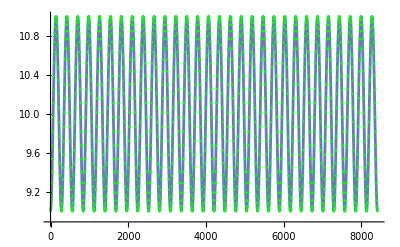

```mathematica
Show[{ListPlot[Table[{t[coft[teval]],r[coft[teval]]},{teval,0,durationN1,deltaT}],Joined->True],
ListPlot[Table[{t[coft[teval]],r[coft[teval]]},{teval,0,durationN1,adjustedDeltaT}],PlotStyle->{Green}]}]
```

```mathematica
filename="trajectory_data_t.dat";
```

```mathematica
arrayData=Table[{t[coft[teval]],r[coft[teval]],ph[coft[teval]],fourvel[coft[teval]]},{teval,0,durationN1,adjustedDeltaT}];
```

```mathematica
Export[filename, arrayData]
```

trajectory_data_t.dat